## Styling

```mathematica
dir=NotebookDirectory[]
```

/home/nicolas/git/talks/ICQ13 September 2016/img/

```mathematica
(* Thickness *)
th=0.003;
```

```mathematica
(*Styling of the text*)
st=Directive[FontSize->10,FontFamily->"CMU Serif"];
stylize[text_]:=Style[text,st];
```

```mathematica
BostonBlue=RGBColor["#00688B"];
comp=RGBColor["#8B2300"];
```

```mathematica
Style[Text["caca"],BostonBlue]
```

caca

## Hamiltonian written in the co basis

```mathematica
(* periodic *)
hp[n_,ρ_]:=Block[{F0=Fibonacci[n-2],F1=Fibonacci[n-1],F2=Fibonacci[n],tblw,tbls,ar},
tblw=Table[{i,i+F0}->ρ,{i,1,F1}];
tbls=Table[{i,i+F1}->1.,{i,1,F0}];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+Transpose[ar]]
]

(* antiperiodic *)
ha[n_,ρ_]:=Block[{F0=Fibonacci[n-2],F1=Fibonacci[n-1],F2=Fibonacci[n],tblw,tbls,ar},
tblw=Table[{i,i+F0}->ρ,{i,2,F1}];
tbls=Table[{i,i+F1}->1.,{i,1,F0}];
PrependTo[tblw,{1,1+F0}->-ρ];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
(* return a list {lower, upper} *)
bands[n_,ρ_]:=Block[{vp, va},
vp=Sort[Eigenvalues[hp[n,ρ]]];
va=Sort[Eigenvalues[ha[n,ρ]]];

MapThread[{Min[#1,#2],Max[#2,#1]}&,{vp, va}]
]
```

## Graphics of the bands of a finite-size system

```mathematica
(* return a list of rectangles, each representing a band *)
ToRectangles[bands_,height_,zero_]:=Map[Rectangle[{#[[1]], -height/2-zero},{#[[2]], height/2-zero}]&,bands]
```

```mathematica
successiveBands=Table[ToRectangles[bands[i+2,0.9], 0.3,i],{i,0,7}];
```

```mathematica
Fibonacci[3]
```

2

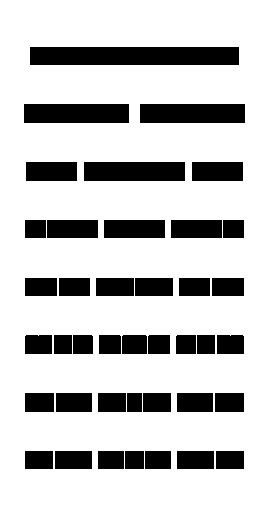

```mathematica
Graphics[successiveBands]
```

## Testing G_n(q)=q F_(n-2) + p F_n

```mathematica
(* select points that can be valid gap labels *)
valid[n_,pt_]:=If[0<pt<Fibonacci[n],pt];
```

```mathematica
(* generate the list p Subscript[F, n] + q Subscript[F, n-2] for p, q in -L, L *)
gen[n_,L_]:=Block[{s=Fibonacci[n],t=Fibonacci[n-2]},
Flatten[Table[p s + q t,{p,-L,L},{q,-L,L}]]]
```

```mathematica
n=9;
L=Fibonacci[n];
valid[n,#]&/@gen[n,L];
DeleteDuplicates[DeleteCases[%,Null]]//Sort
L
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33}

34

```mathematica
(* gap label for the finite size Subscript[F, n] system *) 
G[n_,q_]:=Mod[q Fibonacci[n-1],Fibonacci[n]];
```

```mathematica
n=10;
L=Fibonacci[n];
gaps=Table[{G[n,q],q},{q,0,L-1}];
```

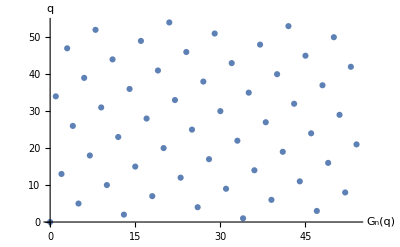

```mathematica
ListPlot[gaps,Filling->None,AspectRatio->1/GoldenRatio,AxesLabel->{"G_n(q)","q"}]
```

```mathematica
n=14;
L=Fibonacci[n];
(* gap widths *)
(*widths=Map[Abs[#[[2]]-#[[1]]]&,bands[n,0.5]];*)
bl=bands[n,0.5];
widths= Table[bl[[g+1,1]]-bl[[g,2]],{g,L-1}];
widths/=Min[widths];
(* gaps as circles in the (q, G(q)) plane, with radii reflecting the width of the gap *)
gapPts=Table[Disk[{G[n,q],If[q<Floor[L/2],q,q-L]},Abs@Log[widths[[G[n,q]]]]],{q,1,L-1}];
```

```mathematica
Graphics[gapPts,Frame->True,FrameLabel->stylize/@{"g_n(q)","q"}]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"q_gq.pdf",%]
```

Export::nodir: Directory /home/nicolas/git/talks/ICQ13 September 2016/img/img/ does not exist.

Export::noopen: Cannot open /home/nicolas/git/talks/ICQ13 September 2016/img/img/q_gq.pdf.

$Failed

## Transient and stable gaps

```mathematica
(* susbstitution matrix *)
Ω={{1,1},{1,0}};
d=Inverse[Ω];
dm=d.d;
da=dm.d;
```

```mathematica
(* iterative construction of the gaps *)
lmol[g_]:=dm.g;
atom[g_]:=da.g+{1,-1};
rmol[g_]:=lmol[g]+{0,1};
(* count the number of states below gap g *)
count[g_,n_]:=g.{Fibonacci[n],Fibonacci[n-1]};
```

```mathematica
(* recursive labelling *)
recur[glist_]:=Flatten[Through[{lmol,atom,rmol}[#]]&/@glist,1]
```

```mathematica
(* initial conditions *)
(* initial transient gap at idos = 1/2 for the chain Subscript[F, 3] = 2 *)
G1={};
G2={};
g0={0,1};
G3={g0};
(* initial stable gaps at idos = 1/3, 2/3 for the chain Subscript[F, 4] = 3 *)
gr={0,1};
gl={1,-1};
G4={gl,gr};
(* Subscript[G, 5] *)
G5={{-1,2},gl,gr,{2,-2}};
(* return the list of gaps at step n (ordered by incresing energy) from the ordered list of gaps at step n-2 and n-3 *)
Gn[{Gm_,Ga_}]:=Join[lmol/@Gm,{gl},atom/@Ga,{gr},rmol/@Gm];
(* take {Subscript[G, n-3],Subscript[G, n-2],Subscript[G, n-1]}, return {Subscript[G, n-2],Subscript[G, n-1],Subscript[G, n]} *)
recurall[{Gn3_,Gn2_,Gn1_}]:={Gn2,Gn1,Gn[{Gn2,Gn3}]}
```

Gap labeling coincides with conumbering

```mathematica
i=5;
Nest[recurall,{G1,G2,G3},i]//Last
(* count the number of states below each gap: check that the gaps are indeed unemerated by increasing value of idos *)
count[#,i+3]&/@%
```

{{5,-8},{-3,5},{2,-3},{7,-11},{-1,2},{4,-6},{-4,7},{1,-1},{6,-9},{-2,4},{3,-4},{8,-12},{0,1},{5,-7},{-3,6},{2,-2},{7,-10},{-1,3},{4,-5},{-4,8}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
lbl[n_,m_]:=Block[{co=G[n,m],L=Fibonacci[n]},
If[co<Floor[L/2],co,co-L]]
```

```mathematica
lbl[8,#]&/@Range[20]
```

{-8,5,-3,-11,2,-6,7,-1,-9,4,-4,9,1,-7,6,-2,-10,3,-5,8}

```mathematica
(* return only the stable gaps *)
Nest[recur,G4,1]
```

{{2,-3},{-2,4},{2,-2},{-1,2},{3,-4},{-1,3}}

```mathematica
i=2;
(* list only the stable gaps *)
G3st={};
G4st=G4;
G5st=G4;
(* list only the transient gaps *)
G3tr=G3;
G4tr={};
G5tr={{-1,2},{2,-2}};
(* for transient gaps we have to remove the gl and gr gaps from the iteration function *)
Gntr[{Gm_,Ga_}]:=Join[lmol/@Gm,atom/@Ga,rmol/@Gm];
(* take {Subscript[G, n-3],Subscript[G, n-2],Subscript[G, n-1]}, return {Subscript[G, n-2],Subscript[G, n-1],Subscript[G, n]} *)
recurtr[{Gn3_,Gn2_,Gn1_}]:={Gn2,Gn1,Gntr[{Gn2,Gn3}]}
(* return only the stable gaps *)
Nest[recurall,{G3st,G4st,G5st},i]//Last;
count[#,i+5]&/@%
Nest[recurtr,{G3tr,G4tr,G5tr},i]//Last;
count[#,i+5]&/@%
```

{2,3,5,6,7,8,10,11}

{1,4,9,12}

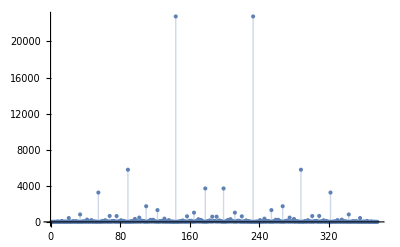

```mathematica
ListPlot[widths,PlotRange->All,Filling->Axis]
```

```mathematica
n=17;
i=n-5;(* number of iterations required *)
stablegaps=Nest[recurall,{G3st,G4st,G5st},i]//Last;
cc=count[#,n]&/@stablegaps;
L=Fibonacci[n];
(* gap widths *)
(*widths=Map[Abs[#[[2]]-#[[1]]]&,bands[n,0.5]];*)
bl=bands[n,.5];
widths= Table[bl[[g+1,1]]-bl[[g,2]],{g,L-1}];
widths/=Min[widths];
(* gaps as circles in the (q, G(q)) plane, with radii reflecting the width of the gap *)
gapPts=Table[If[MemberQ[cc,G[n,q]],{BostonBlue,Disk[{G[n,q],If[q<Floor[L/2],q,q-L]},Abs@Log[widths[[G[n,q]]]]]},{comp,Disk[{G[n,q],If[q<Floor[L/2],q,q-L]},Abs@Log[widths[[G[n,q]]]]]}],{q,1,L-1}];
```

```mathematica
Graphics[gapPts,Frame->True,FrameTicks->None,FrameLabel->stylize/@{"idos","q"},AspectRatio->1]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"q_gq.pdf",%]
Export[NotebookDirectory[]<>"q_gq.png",%%,ImageResolution->200]
```

/home/nicolas/git/talks/ICQ13 September 2016/img/q_gq.pdf

/home/nicolas/git/talks/ICQ13 September 2016/img/q_gq.png

```mathematica
Mag=10;
gapPts3D=Table[If[MemberQ[cc,G[n,q]],{BostonBlue,Point[{G[n,q],If[q<Floor[L/2],q,q-L],Mag Abs@Log[widths[[G[n,q]]]]}]},{comp,Point[{G[n,q],If[q<Floor[L/2],q,q-L],Mag Abs@Log[widths[[G[n,q]]]]}]}],{q,1,L-1}];
```

```mathematica
Graphics3D[gapPts3D];
```

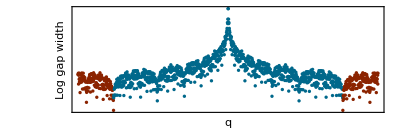

/home/nicolas/git/talks/ICQ13 September 2016/img/q_gapwidth.pdf

/home/nicolas/git/talks/ICQ13 September 2016/img/q_gapwidth.png

```mathematica
gapPts2D=Table[If[MemberQ[cc,G[n,q]],{BostonBlue,Point[{If[q<Floor[L/2],q,q-L],Abs@Log[widths[[G[n,q]]]]}]},{comp,Point[{If[q<Floor[L/2],q,q-L],Abs@Log[widths[[G[n,q]]]]}]}],{q,1,L-1}];
Graphics[{PointSize[0.006],gapPts2D},Frame->True,FrameTicks->None,FrameLabel->stylize/@{"q","Log gap width"},AspectRatio->1/3]
Export[NotebookDirectory[]<>"q_gapwidth.pdf",%]
Export[NotebookDirectory[]<>"q_gapwidth.png",%%,ImageResolution->200]
```

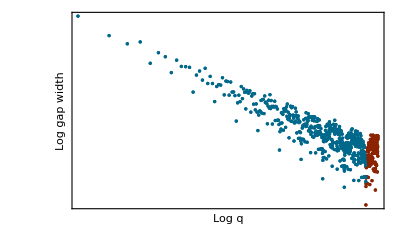

/home/nicolas/git/talks/ICQ13 September 2016/img/logq_gapwidth.pdf

```mathematica
gapPts2D=Table[If[MemberQ[cc,G[n,q]],{BostonBlue,Point[{Log@Abs@If[q<Floor[L/2],q,q-L],Abs@Log[widths[[G[n,q]]]]}]},{comp,Point[{Log@Abs@If[q<Floor[L/2],q,q-L],Abs@Log[widths[[G[n,q]]]]}]}],{q,1,L-1}];
Graphics[{PointSize[0.006],gapPts2D},Frame->True,FrameTicks->None,FrameLabel->stylize/@{"Log q","Log gap width"},AspectRatio->1/GoldenRatio]
Export[NotebookDirectory[]<>"logq_gapwidth.pdf",%]
```

### Plot bands and gap labels (numerical)

```mathematica
ToRectangles[bands[i+2,0.9], 0.3,i];
```

```mathematica
n=6;
i=n-5;(* number of iterations required *)
stablegaps=Nest[recurall,{G3st,G4st,G5st},i]//Last;
transientgaps=Nest[recurtr,{G3tr,G4tr,G5tr},i]//Last;
cc=count[#,n]&/@stablegaps;
L=Fibonacci[n];
(* gap widths *)
(*widths=Map[Abs[#[[2]]-#[[1]]]&,bands[n,0.5]];*)
bl=bands[n,0.5];
widths= Table[bl[[g+1,1]]-bl[[g,2]],{g,L-1}];
widths/=Min[widths];
(* gaps as circles in the (q, G(q)) plane, with radii reflecting the width of the gap *)
gapPts=Table[If[MemberQ[cc,G[n,q]],{BostonBlue,Disk[{G[n,q],If[q<Floor[L/2],q,q-L]},Abs@Log[widths[[G[n,q]]]]]},{comp,Disk[{G[n,q],If[q<Floor[L/2],q,q-L]},Abs@Log[widths[[G[n,q]]]]]}],{q,1,L-1}];
```

```mathematica
(* label gaps *)
ToText[bands_,g_,n_,y0_,s_]:=Block[{c=count[g,n],x0},
x0=(bands[[c,2]]+bands[[c+1,1]])/2;
{FontSize->s,Text[g,{x0,y0}]}]
(* label idos *)
CountTxt[bands_,g_,n_,y0_,s_]:=Block[{c=count[g,n],x0},
x0=(bands[[c,2]]+bands[[c+1,1]])/2;
{FontSize->s,Text[ToString[c]<>"/"ToString[Fibonacci[n]],{x0,y0}]}]
```

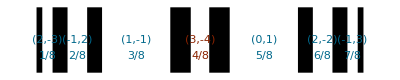

```mathematica
rects=ToRectangles[bl, 0.2,0];

(* label gaps *)
GapToText[bands_,g_,n_,y0_]:=Block[{c=count[g,n],x0},
x0=(bands[[c,2]]+bands[[c+1,1]])/2;
stylize@Text["("<>ToString[g[[1]]]<>","<>ToString[g[[2]]]<>")",{x0,y0}]]
(* label idos *)
IdosToTxt[bands_,g_,n_,y0_]:=Block[{c=count[g,n],x0},
x0=(bands[[c,2]]+bands[[c+1,1]])/2;
stylize[Text[ToString[c]<>"/"<>ToString[Fibonacci[n]],{x0,y0}]]]
(* just print q *)
qToText[bands_,g_,n_,y0_]:=Block[{c=count[g,n],x0,q=g[[2]],qlabel},
x0=(bands[[c,2]]+bands[[c+1,1]])/2;
If[q≥0,qlabel=ToString[q],qlabel=OverBar[ToString[Abs[q]]]];
stylize@Text[qlabel,{x0,y0}]]

txtstable=GapToText[bl,#,n,0]&/@stablegaps;
countstable=IdosToTxt[bl,#,n,-0.05]&/@stablegaps;
txttr=GapToText[bl,#,n,0]&/@transientgaps;
counttr=IdosToTxt[bl,#,n,-0.05]&/@transientgaps;
Graphics[{rects,{BostonBlue,txtstable,countstable},{comp,txttr,counttr}}]
```

```mathematica
Export[NotebookDirectory[]<>"stable_transient.pdf",%]
```

/home/nicolas/git/talks/ICQ13 September 2016/img/stable_transient.pdf

### Plot bands and gap labels (using the RG transformations)

```mathematica
rect[{x1_,x2_},δ_]:=Rectangle[{x1,-δ/2},{x2,+δ/2}];
```

```mathematica
(* takes spectra at step n-3 (g3), n-2 (g2) and n-1 (g1) and return spectra at step n-2, n-1 and n *)
rec[{g3_,g2_,g1_},ts_,tw_]:=Block[{z=tw/(2ts),zb=(tw/ts)^2,g},
g=Flatten [{zb g3,z g2 +ts,z g2 -ts},1];
{g2,g1,g}]
```

```mathematica
ts=1;
tw=0.5;
(* first three spectra corresponding resp to approximants ts, tw and twts *)
g0={{-2ts,2ts}};
g1={{-2tw,2tw}};
g2={{-ts-tw,-ts+tw},{ts-tw,ts+tw}};
```

```mathematica
printGaps[n_]:=Block[{spec,rects,i=n-2,stablegaps,transientgaps,txtstable,txttr},
(* compute the spectrum *)
spec=Nest[rec[#,ts,tw]&,{g0,g1,g2},n]//Last;
spec=Sort[spec];
rects=rect[#,0.2]&/@spec;
(* compute the gap labels *)
stablegaps=Nest[recurall,{G3st,G4st,G5st},i]//Last;
transientgaps=Nest[recurtr,{G3tr,G4tr,G5tr},i]//Last;

txtstable=qToText[spec,#,i+5,0]&/@stablegaps;
txttr=qToText[spec,#,i+5,0]&/@transientgaps;
{rects,{BostonBlue,txtstable},{comp,txttr}}
]
```

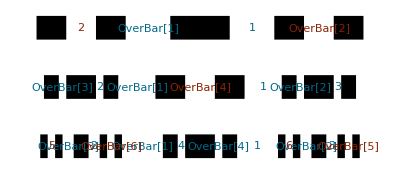

```mathematica
δ=0.5;
Graphics@Table[Translate[printGaps[i],{0,- δ i}],{i,2,4}]
```

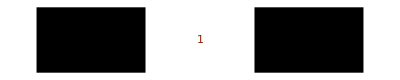

```mathematica
spec3=Sort[g2];
rect3=rect[#,0.2]&/@spec3;
st3=qToText[spec3,#,3,0]&/@G3;
show3={rect3,{comp,st3}};
Graphics[show3]
```

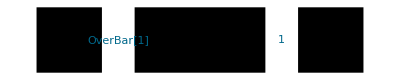

```mathematica
spec4=Sort[Last[rec[{g0,g1,g2},ts,tw]]];
rect4=rect[#,0.2]&/@spec4;
st4=qToText[spec4,#,4,0]&/@G4;
show4={rect4,{BostonBlue,st4}};
Graphics[show4]
```

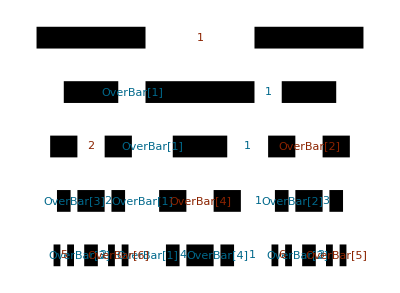

```mathematica
st=Directive[FontSize->10,FontFamily->"CMU Serif"];
δ=0.5;
Graphics[{show3,Translate[show4,{0,-δ}],Table[Translate[printGaps[i],{0,- δ i}],{i,2,4}]}]
```

```mathematica
Export[NotebookDirectory[]<>"gap_labels.pdf",%]
Export[NotebookDirectory[]<>"gap_labels.png",%%,ImageSize->600]
```

/home/nicolas/git/talks/ICQ13 September 2016/img/gap_labels.pdf

/home/nicolas/git/talks/ICQ13 September 2016/img/gap_labels.png

### Fraction transient/stable

```mathematica
i=30;
stablegaps=Nest[recurall,{G3st,G4st,G5st},i]//Last;
transientgaps=Nest[recurtr,{G3tr,G4tr,G5tr},i]//Last;
Length[transientgaps]/Length[stablegaps]//N
```

0.309017

```mathematica
(Length[transientgaps])/(Length[transientgaps]+Length[stablegaps])//N
```

0.236068

## n fixed, vary state (idos)

```mathematica
ρ=0.5;
n=20;
{val,vec}=Eigensystem[hco[n,ρ]];
```

Set::shape: Lists {val,vec} and Eigensystem[hco[20,0.5]] are not the same shape.

```mathematica
o=Ordering[val];
val=val[[o]];
vec=vec[[o]];
```

Ordering::normal: Nonatomic expression expected at position 1 in Ordering[val].

Part::pkspec1: The expression Ordering[val] cannot be used as a part specification.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of val⟦Ordering[val]⟧.

```mathematica
Length[val]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of val⟦Ordering[val]⟧.

Hold[Length[val]]

```mathematica
ListPlot[val,Joined->True]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of val⟦Ordering[val]⟧.

Hold[ListPlot[val,Joined→True]]

```mathematica
(* chose a state *)
a=5000;
s=Abs[vec[[a]]];
(* random variable *)
x=Log[s];
```

Part::partd: Part specification vec⟦5000⟧ is longer than depth of object.

```mathematica
Histogram[s,Automatic,"Probability"]
```

Histogram::ldata: Abs[vec⟦5000⟧] is not a valid dataset or list of datasets.

Histogram[Abs[vec⟦5000⟧],Automatic,Probability]

```mathematica
{x0,σ}={Mean[x],StandardDeviation[x]};
```

```mathematica
logn[t_]:=Exp[-(t-x0)^2/(2σ)];
norm=1/Integrate[logn[t],{t,-10,0}];
```

```mathematica
Histogram[x,{-15,0,0.55},"Probability",Epilog->First@Plot[0.65*norm logn[x],{x,-12,-1},PlotRange->All]]
```

Histogram::ldata: Log[Abs[vec⟦5000⟧]] is not a valid dataset or list of datasets.

Histogram[Log[Abs[vec⟦5000⟧]],{-15,0,0.55},Probability,Epilog→{{},{}}]

```mathematica
{x0,σ}={Mean[x],StandardDeviation[x]};
```

```mathematica
Plot[Exp[-(Log[x]-x0)^2/(2σ)],{x,0,0.035},PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[s,Joined->False,PlotRange->All]
```

ListPlot::lpn: Abs[vec⟦5000⟧] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot[Abs[vec⟦5000⟧],Joined→False,PlotRange→All]

```mathematica
Histogram[Log[Abs[Flatten[vec]]],Automatic,"Probability"]
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[vec].

Histogram::ldata: Log[Abs[Flatten[vec]]] is not a valid dataset or list of datasets.

Histogram[Log[Abs[Flatten[vec]]],Automatic,Probability]

## idos fixed, vary n

```mathematica
ρ=0.5;
n=20;
{valp,vecp}=Eigensystem[hco[n,ρ]];
{val,vec}=Eigensystem[hco[n-1,ρ]];
```

Set::shape: Lists {valp,vecp} and Eigensystem[hco[20,0.5]] are not the same shape.

Set::shape: Lists {val,vec} and Eigensystem[hco[19,0.5]] are not the same shape.

```mathematica
o=Ordering[val];
val=val[[o]];
vec=vec[[o]];

o=Ordering[valp];
valp=valp[[o]];
vecp=vecp[[o]];

L=Fibonacci[n-1];
Lp=Fibonacci[n];

idos=Table[{val[[i]],N[i/L]},{i,L}];
idosp=Table[{valp[[i]],N[i/Lp]},{i,Lp}];
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of val⟦Ordering[val]⟧.

Ordering::normal: Nonatomic expression expected at position 1 in Ordering[valp].

Part::pkspec1: The expression Ordering[valp] cannot be used as a part specification.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of valp⟦Ordering[valp]⟧.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of val⟦Ordering[val]⟧.

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of valp⟦Ordering[valp]⟧.

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

```mathematica
(* chose a gap ie an energy label on the small chain *)
g=2000;
(* corresponding energy label on the large chain *)
gp=Floor[g Lp/L];

(* the 2 corresponding states *)
s=Abs[vec[[g]]];
sp=Abs[vecp[[gp]]];
```

Part::partd: Part specification vec⟦2000⟧ is longer than depth of object.

Part::partd: Part specification vecp⟦3236⟧ is longer than depth of object.

```mathematica
(* do the 2 states look different? *)
sx=Table[{i/L,s[[i]]},{i,L}];
spx=Table[{i/Lp,sp[[i]]},{i,Lp}];
ListPlot[{sx,spx},PlotRange->All]
```

Part::partw: Part 2 of Abs[vec⟦2000⟧] does not exist.

Part::partw: Part 3 of Abs[vec⟦2000⟧] does not exist.

Part::partw: Part 4 of Abs[vec⟦2000⟧] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 2 of Abs[vecp⟦3236⟧] does not exist.

Part::partw: Part 3 of Abs[vecp⟦3236⟧] does not exist.

Part::partw: Part 4 of Abs[vecp⟦3236⟧] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"data/consecutive_sizes_state.png",%,ImageSize->1000]
```

Export::nodir: Directory /home/nicolas/git/talks/ICQ13 September 2016/img/data/ does not exist.

Export::noopen: Cannot open /home/nicolas/git/talks/ICQ13 September 2016/img/data/consecutive_sizes_state.png.

$Failed

```mathematica
{Histogram[s,Automatic,"Probability"],Histogram[sp,Automatic,"Probability"]}
```

Histogram::ldata: Abs[vec⟦2000⟧] is not a valid dataset or list of datasets.

Histogram::ldata: Abs[vecp⟦3236⟧] is not a valid dataset or list of datasets.

{Histogram[Abs[vec⟦2000⟧],Automatic,Probability],Histogram[Abs[vecp⟦3236⟧],Automatic,Probability]}

```mathematica
x=Log[s];
xp=Log[sp];
{x0,σ}={Mean[x],StandardDeviation[x]};
{x0p,σp}={Mean[xp],StandardDeviation[xp]};
```

```mathematica
logn[t_]:=Exp[-(t-x0)^2/(2σ)];
norm=1/Integrate[logn[t],{t,-10,0}];
lognp[t_]:=Exp[-(t-x0p)^2/(2σp)];
normp=1/Integrate[lognp[t],{t,-10,0}];
```

```mathematica
Histogram[x,{-15,0,0.55},"Probability",Epilog->First@Plot[0.5*norm logn[x],{x,-12,-1},PlotRange->All]]
Histogram[xp,{-15,0,0.55},"Probability",Epilog->First@Plot[0.5*normp lognp[x],{x,-12,-1},PlotRange->All]]
```

Histogram::ldata: Log[Abs[vec⟦2000⟧]] is not a valid dataset or list of datasets.

Histogram[Log[Abs[vec⟦2000⟧]],{-15,0,0.55},Probability,Epilog→{{},{}}]

Histogram::ldata: Log[Abs[vecp⟦3236⟧]] is not a valid dataset or list of datasets.

Histogram[Log[Abs[vecp⟦3236⟧]],{-15,0,0.55},Probability,Epilog→{{},{}}]

```mathematica
Export[NotebookDirectory[]<>"data/plogpsi.png",%,ImageSize->1000]
```

Export::nodir: Directory /home/nicolas/git/talks/ICQ13 September 2016/img/data/ does not exist.

Export::noopen: Cannot open /home/nicolas/git/talks/ICQ13 September 2016/img/data/plogpsi.png.

$Failed